```mathematica
Needs["PlotLegends`"];
SetOptions[ListPlot,BaseStyle->{FontFamily->"Times",FontSize->14}];
```

```mathematica
SetDirectory["C:\Documents and Settings\gyue\Desktop\Research\ic-flux-modullation"];
I0=4.6*10^(-6);ϕ0=2.067833636*10^(-15);L=100*10^(-12);b=ϕ0/2/π/L/I0;
u[x_,y_,s_,yb_,αl_,αi_,b_]:=-s*x-s*αl*y+b(y-yb)^2-b*yb^2-Cos[x]*Cos[y]-αi*Sin[x]*Sin[y];
drawp[s_,yb_,αl_,αi_,b_]:=Plot3D[u[x,y,s,yb,αl,αi,b],{x,0,20},{y,-3,3},AxesLabel->{Style[x,14],Style[y,14],Style["U(x,y)",14]}];
Icflux[αl_,αi_,b_,si_,xi1_,yi1_,xi2_,yi2_,cl_,shift_]:=Module[{xf,yf,sf=si,i,u0,table0,P1,yb,N0,a,x,y,s},
u0[x_,y_]:=u[x,y,s,yb,αl,αi,b];
table0={};
N0=101;
xf=xi1;yf=yi1;sf=si;
For[i=0,i≤N0,i++,
yb=i*0.005*π+shift;
a=FindRoot[{D[u0[x,y],x]==0,D[u0[x,y],y]==0,D[D[u0[x,y],x],x]*D[D[u0[x,y],y],y]-(D[D[u0[x,y],x],y])^2==0},{{s,sf},{x,xf},{y,yf}}];
xf=x/.a;yf=y/.a;sf=s/.a;
table0=Prepend[table0,{yb/π,Abs[s/.a]*I0*10^6}];
table1=Prepend[table1,{yb/π,Abs[s/.a],xf,yf}];
];
xf=xi1;yf=yi1;sf=si;
For[i=0,i≥-N0,i--,
yb=i*0.005*π+shift;
a=FindRoot[{D[u0[x,y],x]==0,D[u0[x,y],y]==0,D[D[u0[x,y],x],x]*D[D[u0[x,y],y],y]-(D[D[u0[x,y],x],y])^2==0},{{s,sf},{x,xf},{y,yf}}];
xf=x/.a;yf=y/.a;sf=s/.a;
table0=Prepend[table0,{yb/π,Abs[s/.a]*I0*10^6}];
table1=Prepend[table1,{yb/π,Abs[s/.a],xf,yf}];
];
xf=xi2;yf=yi2;sf=si;
For[i=0,i≤N0,i++,
yb=i*0.005*π+π+shift;
a=FindRoot[{D[u0[x,y],x]==0,D[u0[x,y],y]==0,D[D[u0[x,y],x],x]*D[D[u0[x,y],y],y]-(D[D[u0[x,y],x],y])^2==0},{{s,sf},{x,xf},{y,yf}}];
xf=x/.a;yf=y/.a;sf=s/.a;
table0=Prepend[table0,{yb/π,Abs[s/.a]*I0*10^6}];
table1=Prepend[table1,{yb/π,Abs[s/.a],xf,yf}];
];
xf=xi2;yf=yi2;sf=si;
For[i=0,i≥-N0,i--,
yb=i*0.005*π+π+shift;
a=FindRoot[{D[u0[x,y],x]==0,D[u0[x,y],y]==0,D[D[u0[x,y],x],x]*D[D[u0[x,y],y],y]-(D[D[u0[x,y],x],y])^2==0},{{s,sf},{x,xf},{y,yf}}];
xf=x/.a;yf=y/.a;sf=s/.a;
table0=Prepend[table0,{yb/π,Abs[s/.a]*I0*10^6}];
table1=Prepend[table1,{yb/π,Abs[s/.a],xf,yf}];
];
Export["aa.txt",table1,"Table"];
P1=ListPlot[table0,PlotStyle->Directive[cl,PointSize[0.005]],GridLines->Automatic,Frame->True,ImageSize->800]
];
cri:=D[D[u[x,y,s,yb,0,0.3,b],x],x]+D[D[u[x,y,s,yb,0,0,b],y],y];
```

```mathematica
drawp[1,0.1,-0.3,0.1,b]
```

-Graphics3D-

```mathematica
table1={};cri
```

1.4309+2 Cos[x] Cos[y]+0.3 Sin[x] Sin[y]

```mathematica
line=Line[{{0,0},{3,0}}]
```

Line[{{0,0},{3,0}}]

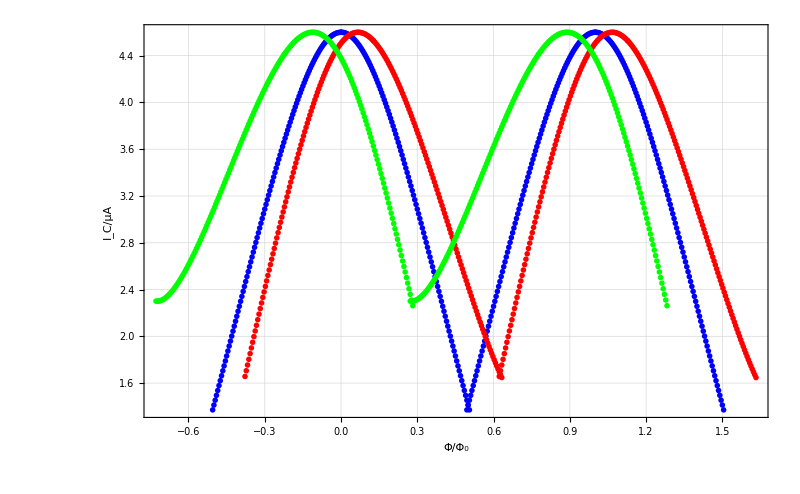

```mathematica
P1=Icflux[0,0,b,1,-4,0,3,3,Blue,0];
P2=Icflux[0,0.3,b,1,4,0,9,3,Red,0.4];
P3=Icflux[0,0.5,b,1,13.5,0,10,3,Green,-0.7];
ShowLegend[Show[P1,P2,P3,FrameLabel->{"Φ/Φ_0","I_C/μA"}],{{{Graphics[{Blue,line}],Style["α_I=0",14]},{Graphics[{Red,line}],Style["α_I=0.3",14]},{Graphics[{Green,line}],Style["α_I=0.5",14]}},LegendPosition->{1.1,-0.2},LegendShadow->None,LegendSize->0.25}]
```

```mathematica
cri
```

1.4309+2 Cos[x] Cos[y]+0.3 Sin[x] Sin[y]

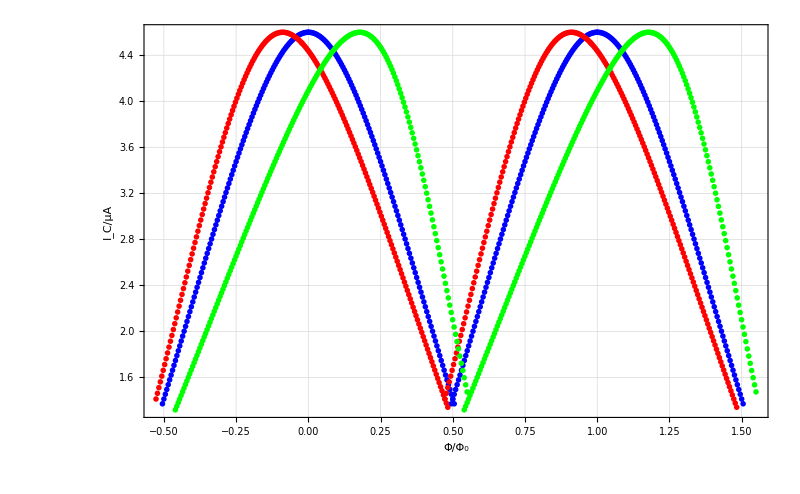

```mathematica
P1=Icflux[0,0,b,1,-4,0,3,3,Blue,0];
P2=Icflux[0.4,0,b,1,6,0,16.5,3,Red,-0.07];
P3=Icflux[0.8,0,b,1,6,0,3,3,Green,0.14];
ShowLegend[Show[P1,P2,P3,FrameLabel->{"Φ/Φ_0","I_C/μA"}],{{{Graphics[{Blue,line}],Style["α_L=0",14]},{Graphics[{Red,line}],Style["α_L=0.4",14]},{Graphics[{Green,line}],Style["α_L=0.8",14]}},LegendPosition->{1.1,-0.2},LegendShadow->None,LegendSize->0.25}]
```

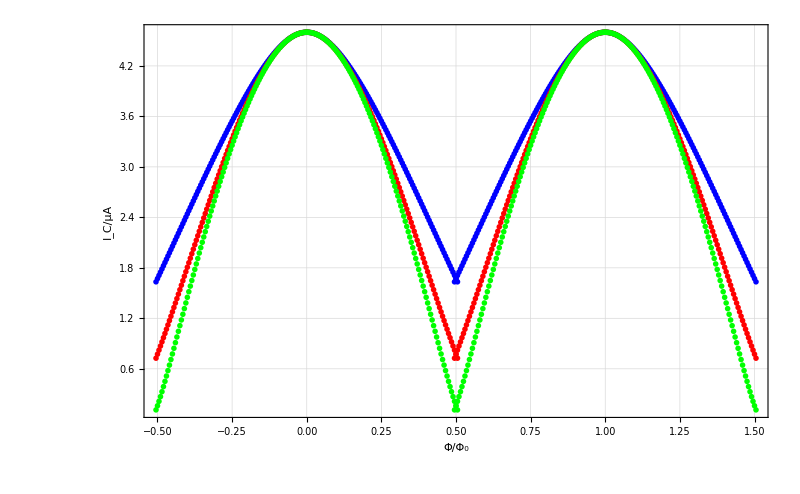

```mathematica
P1=Icflux[0,0,0.8*b,1,-4,0,3,3,Blue,0];
P2=Icflux[0,0,2*b,1,6,0,16.5,3,Red,0];
P3=Icflux[0,0,10*b,1.1,6,0,3,3,Green,0];
ShowLegend[Show[P1,P2,P3,FrameLabel->{"Φ/Φ_0","I_C/μA"}],{{{Graphics[{Blue,line}],Style["L=125pH",14]},{Graphics[{Red,line}],Style["L=50pH",14]},{Graphics[{Green,line}],Style["L=10pH",14]}},LegendPosition->{1.1,-0.2},LegendShadow->None,LegendSize->0.35}]
```

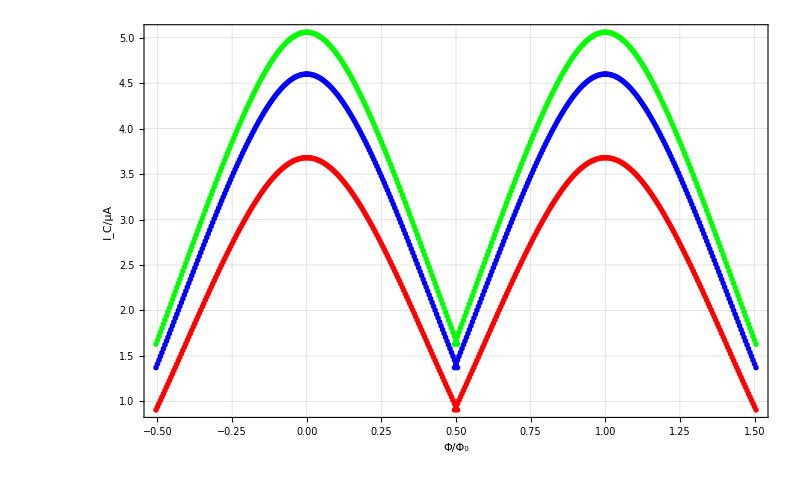

```mathematica
I0=4.6*10^(-6);ϕ0=2.067833636*10^(-15);L=100*10^(-12);b=ϕ0/2/π/L/I0;
P1=Icflux[0,0,b,1,-4,0,3,3,Blue,0];
I0=0.8I0;
ϕ0=2.067833636*10^(-15);L=100*10^(-12);b=ϕ0/2/π/L/I0;
P2=Icflux[0,0,b,1,-4,0,3,3,Red,0];
I0=I0/0.8*1.1;
ϕ0=2.067833636*10^(-15);L=100*10^(-12);b=ϕ0/2/π/L/I0;
P3=Icflux[0,0,b,1,-4,0,3,3,Green,0];
ShowLegend[Show[P1,P2,P3,FrameLabel->{"Φ/Φ_0","I_C/μA"}],{{{Graphics[{Blue,line}],Style["Ic=I0",14]},{Graphics[{Red,line}],Style["Ic=0.8I0",14]},{Graphics[{Green,line}],Style["Ic=1.1I0",14]}},LegendPosition->{1.1,-0.2},LegendShadow->None,LegendSize->0.35}]
```